```mathematica
filenameVolumeBase="FR96G1_";
pathVolumesFitted="/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/Downsample_by2/"
concFRG1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_2.5microns.h5",{"Datasets","concFR"}];
Dimensions[concFRG1]
```

/melete-nas01/lsu/scratch/olatinwo/CAMD_Nov2012/Downsample_by2/

{256,352,615}

```mathematica
filenameVolumeBase="FR96G2_";
concFRG2=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_2.5microns.h5",{"Datasets","concFR"}];
Dimensions[concFRG2]
```

{256,611,507}

```mathematica
filenameVolumeBase="FR96F1_";
concFRF1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_2.5microns.h5",{"Datasets","concFR"}];
Dimensions[concFRF1]
```

{256,631,612}

```mathematica
filenameVolumeBase="FR96E1_";
concFRE1=Import[pathVolumesFitted<>filenameVolumeBase<>"vol_percent_MF1_FR_2.5microns.h5",{"Datasets","concFR"}];
Dimensions[concFRE1]
```

{256,723,705}

```mathematica
SeedRandom[1]; numberOfVoxels=1000000;
listOfNonZeroVoxels = Select[Flatten[concFRG1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRG1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRG1]

SeedRandom[1];
listOfNonZeroVoxels = Select[Flatten[concFRG2],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRG2 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRG2]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRF1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRF1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRF1]

SeedRandom[1]; 
listOfNonZeroVoxels = Select[Flatten[concFRE1],#>0&];//Timing
Length[listOfNonZeroVoxels]
concFRE1 = RandomSample[100*listOfNonZeroVoxels,numberOfVoxels];
Length[concFRE1]
```

{30.6923,Null}

24492316

1000000

{44.2193,Null}

38028682

1000000

{54.9816,Null}

61869601

1000000

{72.9479,Null}

79321971

1000000

```mathematica
list =HistogramList[concFRG1,{0.0,100,0.1}];
threshold=5.7;
indexThreshold=Position[list[[1]],p_?(#==threshold&)][[1,1]]
volPercentNumerator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,indexThreshold,Length[list[[1]]]-1}];
volPercentDenominator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,1,Length[list[[1]]]-1}];
volPercentNumerator = Total[volPercentNumerator]
volPercentDenominator = Total[volPercentDenominator]
fractionBFRinlumps = 100*volPercentNumerator/volPercentDenominator
```

58

102100.

4.4372×10^6

2.301

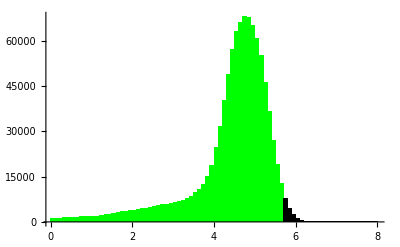

```mathematica
listBelowThreshold = Histogram[Select[concFRG1,#<threshold &],{0.0,8,0.1},ChartStyle->Directive[Green,EdgeForm[]]];
listAboveThreshold = Histogram[Select[concFRG1,#>=threshold &],{0,8,0.1},ChartStyle->Directive[Black,EdgeForm[]]];
gFRG1=Show[{listBelowThreshold,listAboveThreshold}]
```

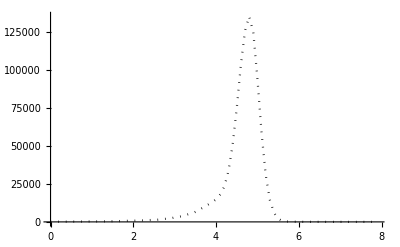

```mathematica
data =HistogramList[concFRG2,{0,8,0.1}];
gFRG2 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dotted]]
```

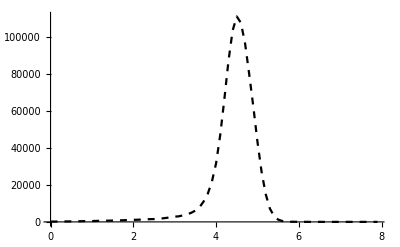

```mathematica
data =HistogramList[concFRF1,{0,8,0.1}];
gFRF1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black,Dashed]]
```

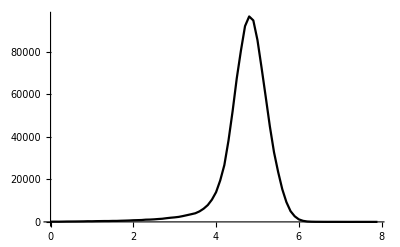

```mathematica
data =HistogramList[concFRE1,{0,8,0.1}];
gFRE1 = ListLinePlot[Transpose[{Drop[data[[1]],-1],data[[2]]}],PlotRange->All,PlotStyle->Directive[Black]]
```

```mathematica
{gFRG2,gFRF1,gFRE1}
```

{-Graphics-,-Graphics-,-Graphics-}

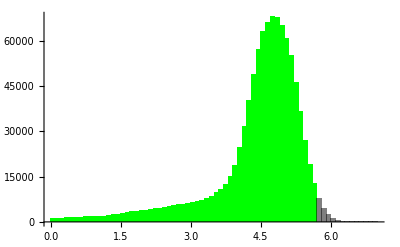

```mathematica
gHistG1=Histogram[{
Select[concFRG1,#<threshold &],
Select[concFRG1,#>=threshold &]},{0,7,.1},
ChartStyle->{ Directive[Green,Opacity[1],EdgeForm[]],Directive[Black,EdgeForm[]]}]
```

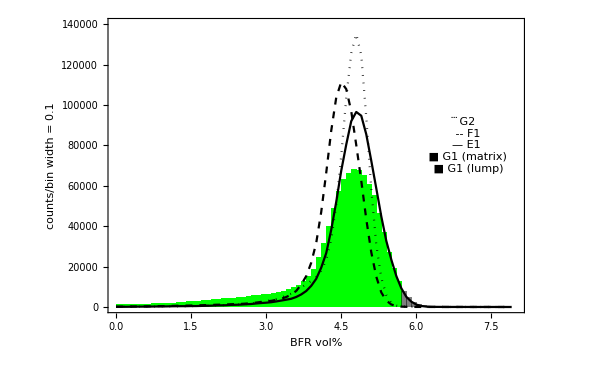

```mathematica
Show[{gHistG1,gFRG2,gFRF1,gFRE1},PlotRange->{{0,8},{0,140000}},
Frame->True,FrameStyle->14,ImageSize->600,
FrameLabel->{{"counts/bin width = 0.1",""},{"BFR vol%",""}},
Epilog->Style[Text[Framed[" ⃛ G2\n -- F1\n— E1\n ■ G1 (matrix)\n ■ G1 (lump)"],{7.0,80000}],16,TextAlignment->Right]]
```

```mathematica
TableForm[
{{"G1", Mean[concFRG1],StandardDeviation[concFRG1],Max[concFRG1]},
{"G2", Mean[concFRG2],StandardDeviation[concFRG2],Max[concFRG2]},
{"F1", Mean[concFRF1],StandardDeviation[concFRF1],Max[concFRF1]},
{"E1", Mean[concFRE1],StandardDeviation[concFRE1],Max[concFRE1]}}, 
TableHeadings->{None,{"sample","average","standard deviation", "maximum"}}]

TableForm[
{{"G1", threshold,fractionBFRinlumps}}, 
TableHeadings->{None,{"sample","threshold","fraction in lumps"}}]
```

sample | average | standard deviation | maximum
G1 | 4.4372 | 0.982033 | 13.886
G2 | 4.6564 | 0.547778 | 14.1878
F1 | 4.47336 | 0.565794 | 14.4457
E1 | 4.77852 | 0.598483 | 20.3507

sample | threshold | fraction in lumps
G1 | 5.7 | 2.301

```mathematica
list =HistogramList[concFRG2,{0.0,100,0.1}];
threshold=4;
indexThreshold=Position[list[[1]],p_?(#==threshold&)][[1,1]]
volPercentNumerator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,indexThreshold,Length[list[[1]]]-1}];
volPercentDenominator = Table[Mean[{list[[1,i]],list[[1,i+1]]}]*list[[2,i]], {i,1,Length[list[[1]]]-1}];
volPercentNumerator = Total[volPercentNumerator]
volPercentDenominator = Total[volPercentDenominator]
fractionBFRinlumps = 100*volPercentNumerator/volPercentDenominator
```

41

4.36186×10^6

4.65641×10^6

93.6744